```mathematica
$Path=Prepend[$Path,"/Users/sumner/Programming/WSS2018/DeepGraphDraw/" ];
<<DeepGraphDraw`
```

# Nets

```mathematica
lecnn="num_v_10_prob_e_0.5_layout_LayeredEmbedding_n_1000000_ratios_{0.7, 0.2, 0.1}_cnn.mx";
lelin="num_v_10_prob_e_0.5_layout_LayeredEmbedding_n_1000000_ratios_{0.7, 0.2, 0.1}_linear.mx";
spcnn="num_v_10_prob_e_0.5_layout_SpringElectricalEmbedding_n_1000000_ratios_{0.7, 0.2, 0.1}_cnn.mx";
splin="num_v_10_prob_e_0.5_layout_SpringElectricalEmbedding_n_1000000_ratios_{0.7, 0.2, 0.1}_linear.mx";
folder="/Users/sumner/Programming/WSS2018/DeepGraphDraw/nets";
```

```mathematica
nets = <|
"lecnn"->Import@FileNameJoin[{folder, lecnn}],
"lelin"->Import@FileNameJoin[{folder, lelin}],
"spcnn"->Import@FileNameJoin[{folder, spcnn}],
"splin"->Import@FileNameJoin[{folder, splin}]
|>;
```

```mathematica
neto=nets["lelin"];
net=neto["TrainedNet"];
```

```mathematica
ledat="num_v_10_prob_e_0.5_layout_LayeredEmbedding_n_1000000_ratios_{0.7, 0.2, 0.1}.mx";
spdat="num_v_10_prob_e_0.5_layout_SpringElectricalEmbedding_n_1000000_ratios_{0.7, 0.2, 0.1}.mx";
datfolder="/Users/sumner/Programming/WSS2018/DeepGraphDraw/data";
```

```mathematica
data=Import[FileNameJoin[{datfolder,ledat}]];
```

```mathematica
n=1;p=9;
rec=Normal[data["TestData"][n;;n+p]];
inp=Normal[data["TestData"][n;;n+p,"Input"]];
out=Normal[data["TestData"][n;;n+p,"Output"]];
```

{CompactErrorRateEvolutionPlot,CompactLossEvolutionPlot,ErrorRateEvolutionPlot,EvolutionPlot,LossEvolutionPlot}

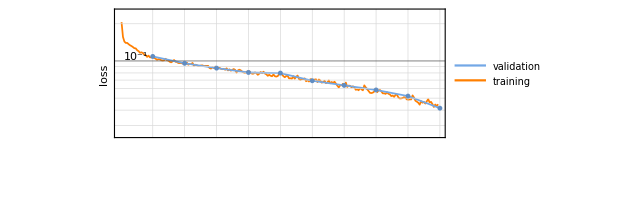

```mathematica
DeleteCases[Flatten[StringCases[neto["Properties"],___~~"Plot"]],{}]
neto["LossEvolutionPlot"]
```

```mathematica
data["TrainingData"]//Length
```

700000

```mathematica
EdgeCrossing
```

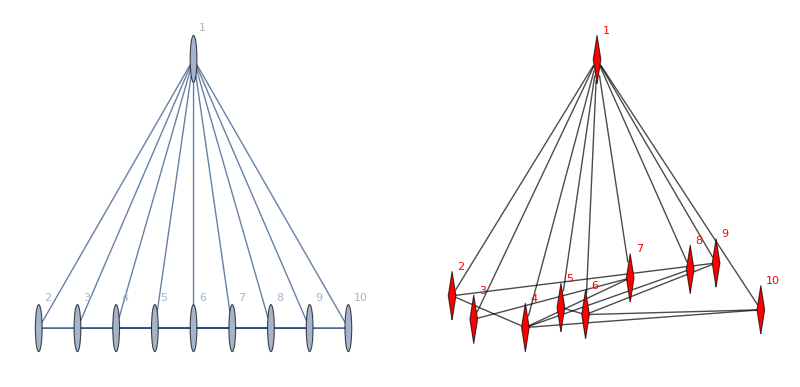
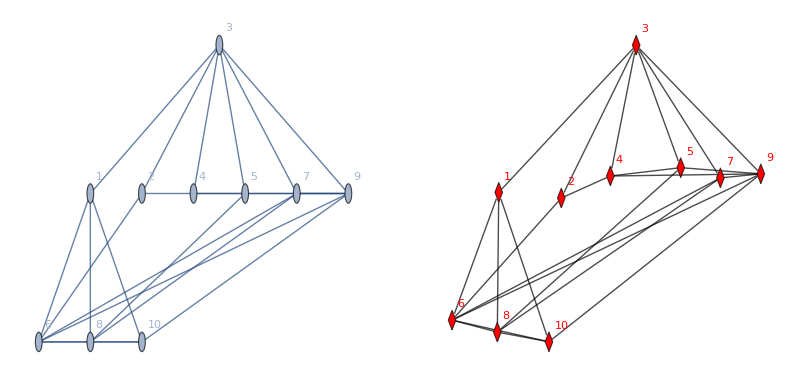
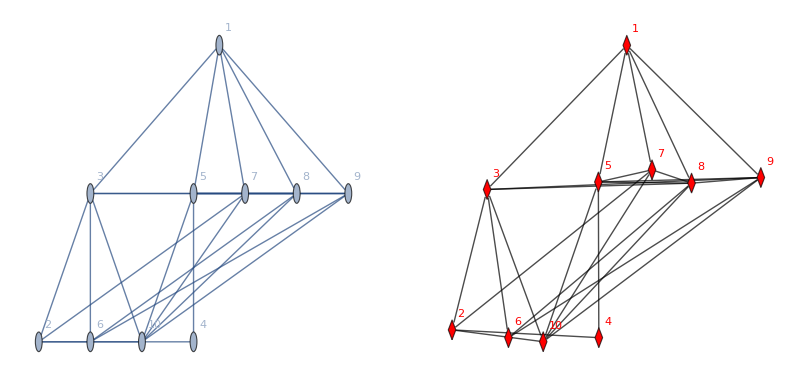
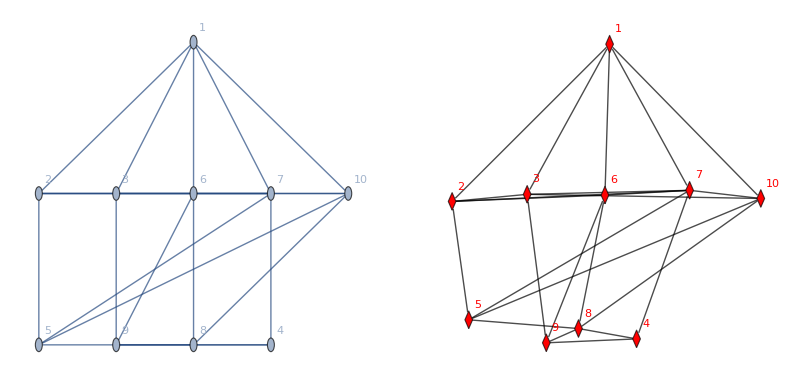

```mathematica
ds="TestData";
rsi=RandomSample[Range[Length@data[ds]],4];
rs=data[ds][rsi];
cfc=CompareForcedCoordinates[
Normal[#["Input"]],
net[ Normal[#["Input"]]],
"PrintReadyQ"->True,
"GraphLayout"-> "LayeredEmbedding"
(*"GraphLayout"->"SpringElectricalEmbedding" (* only effects the original graph's drawing *)*)
]&/@Normal[rs]
```

```mathematica
gg=GraphicsGrid[Partition[cfc,{2}], AspectRatio->1,ImageSize->Full]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"lelin_res_10.svg"}],gg]
Export[FileNameJoin[{NotebookDirectory[],"lelin_res_10.pdf"}],gg]
```

/Users/sumner/Programming/WSS2018/DeepGraphDraw/playgrounds/lelin_res_use.svg

/Users/sumner/Programming/WSS2018/DeepGraphDraw/playgrounds/lelin_res_use.pdf

```mathematica
Directory[]
```

/Users/sumner

```mathematica
(Import@"~/Desktop/matteo.wlnet")[RandomReal[{1},{256,10}]]
```

{{3.77185,5.95636,16.2332,16.3276,0.440617,2.69809,17.4117,7.20866,6.8845,4.72934},{0.0671409,-0.526083,-0.0944594,0.0337352,-0.415896,-0.423625,0.0533351,-0.0627658,-0.10734,-0.313617},{-1.01634,-0.902641,-0.83087,-0.824643,-0.881425,-0.949484,-1.01484,-1.03608,-0.961796,-0.929344},{-1.63341,-1.57889,-1.66249,-1.71641,-1.70306,-1.7254,-1.61667,-1.73967,-1.62899,-1.64703},{14.8784,24.4361,15.9878,14.3713,11.4234,26.4308,17.5549,6.08808,20.7262,26.2486},{19.3321,15.1166,15.5731,0.156501,1.27955,12.9007,3.18315,22.7208,19.9449,14.4246},{-1.05084,-1.12881,-1.19631,-1.09251,-1.18704,-1.21245,-1.11147,-1.13781,-1.15324,-1.03942},{-0.170363,-0.297649,-0.183752,-0.11038,-0.0524378,-0.132255,-0.420865,-0.47123,-0.310895,-0.553511},{-1.11139,-0.987043,-1.05731,-1.12953,-1.04902,-0.98203,-1.02207,-1.17186,-1.15646,-1.13104},{16.2773,22.4026,27.1935,9.31885,27.9482,16.4308,9.04277,11.4071,19.146,10.8248},{22.6505,22.3188,14.5339,29.0899,19.5656,25.4695,21.5722,23.8499,17.7774,10.1256},{-0.61041,-0.540695,-0.589686,-0.566163,-0.538418,-0.624777,-0.583244,-0.637568,-0.581278,-0.624235},{6.82477,19.3701,9.1943,8.81426,8.62184,3.59261,11.8049,10.172,18.3284,9.97454},{14.0907,15.9336,10.1252,10.1886,5.46023,2.78361,4.00198,4.43581,0.719012,10.6263},{10.7076,20.8254,17.0765,1.60382,4.07434,1.6875,14.4227,0.546877,17.076,1.66735},{-1.30482,-1.33248,-1.3982,-1.2529,-1.26567,-1.39307,-1.28823,-1.24935,-1.27731,-1.3324},{4.43043,17.3011,24.6355,4.6445,17.0387,0.653148,28.4023,23.6291,28.6381,4.52502},{-0.908656,-0.989225,-0.880006,-0.958449,-0.955082,-0.974107,-0.961216,-1.01134,-0.919742,-0.922057},{-1.42921,-1.42663,-1.41668,-1.41742,-1.41128,-1.43963,-1.35739,-1.3205,-1.46046,-1.39684},{-0.880644,-0.968401,-0.891725,-0.835418,-0.929715,-0.998035,-0.914209,-0.852887,-0.902754,-0.882544},{-1.75182,-1.70495,-1.6509,-1.76966,-1.62809,-1.60062,-1.7383,-1.77128,-1.64321,-1.64056},{-1.10922,-1.13712,-1.12056,-1.18606,-1.20121,-1.17833,-1.13889,-1.09693,-1.21508,-1.08011},{-1.28954,-1.40519,-1.25534,-1.2728,-1.29641,-1.39895,-1.4118,-1.32804,-1.28993,-1.31753},{2.09759,6.43363,10.7172,22.9467,2.50322,26.5614,1.42748,4.65144,10.2468,9.0213},{2.62437,5.16385,2.79608,4.78025,2.32775,3.70288,2.04952,4.8267,1.16301,1.87852},{-0.687495,-0.685357,-0.611458,-0.521267,-0.631576,-0.562606,-0.56481,-0.528992,-0.685528,-0.680195},{-1.52681,-1.57362,-1.66787,-1.67307,-1.60733,-1.54402,-1.67106,-1.56327,-1.61174,-1.59055},{-1.22317,-1.21731,-1.13014,-1.19767,-1.11092,-1.16988,-1.23013,-1.08486,-1.14656,-1.22772},{15.7306,29.108,25.245,7.80265,20.5747,20.5639,11.7971,11.8908,8.20275,13.8111},{-0.109245,-0.0811701,-0.247537,-0.216362,-0.0286546,-0.262029,-0.0236987,-0.13119,-0.0217341,-0.259985},{8.79121,23.8873,7.64152,14.6227,8.50403,15.4263,20.7606,13.0708,14.6605,12.0886},{8.50661,13.4124,20.0961,14.9927,23.2527,10.9428,10.1282,3.26096,11.5376,10.8887},{2.77822,23.7291,25.4511,3.0949,1.03907,25.5548,6.13501,0.458893,8.41539,14.6067},{13.5203,5.37858,24.5943,6.43316,3.00648,3.77029,5.96436,5.001,24.3624,16.0036},{16.9955,10.2609,-0.190231,27.7816,25.7571,11.1035,28.2677,9.53969,4.82814,4.92197},{-1.3117,-1.27389,-1.25331,-1.28728,-1.1794,-1.17841,-1.27524,-1.20088,-1.27098,-1.18735},{0.265024,0.264364,0.476666,0.876021,0.784192,0.4415,0.0849334,-0.139411,0.588954,0.815124},{-0.982761,-1.07407,-1.05767,-0.938739,-0.987645,-1.06945,-0.962113,-1.02639,-1.00455,-1.03057},{-0.799286,-0.885218,-0.901304,-0.870804,-0.801469,-0.818789,-0.80412,-0.852798,-0.859637,-0.833151},{-1.42842,-1.41761,-1.55289,-1.47171,-1.46585,-1.54659,-1.4699,-1.53816,-1.48674,-1.50362},{-0.625558,-0.623864,-0.625018,-0.740808,-0.616465,-0.689524,-0.721556,-0.727133,-0.641049,-0.741211},{27.6847,25.5111,1.88495,18.0988,13.608,22.6164,29.0737,16.698,2.27706,2.43463},{-1.6931,-1.58144,-1.53407,-1.55358,-1.64645,-1.68497,-1.65292,-1.68016,-1.67859,-1.66424},{5.15613,0.89726,5.51129,5.30988,3.52341,1.60384,3.08408,1.90512,3.73823,1.11106},{-0.610248,-0.394525,-0.379755,-0.491394,-0.494983,-0.49874,-0.490391,-0.481265,-0.530512,-0.504035},{1.36762,1.28834,2.03266,2.34735,0.961268,2.00894,3.40542,2.03719,0.466823,4.01593},{-0.449248,-0.509335,-0.525037,-0.51999,-0.535979,-0.646161,-0.45109,-0.525597,-0.413742,-0.596716},{-0.771571,-0.793499,-0.75806,-0.824267,-0.708214,-0.740174,-0.777753,-0.738219,-0.805912,-0.799382},{-1.90117,-1.89245,-1.73998,-1.77853,-1.88314,-1.92839,-1.84585,-1.83108,-1.88544,-1.78571},{-1.02947,-0.965171,-1.06505,-0.985126,-1.02352,-1.05471,-0.960534,-1.02905,-1.01299,-0.997416},{-0.380791,0.13429,-0.0710632,-0.383072,-0.25229,0.0858055,-0.391643,0.0367564,-0.15433,-0.494482},{28.8786,28.1146,25.0321,9.70676,4.10252,6.86741,27.9243,9.40698,6.72536,18.5616},{-0.169405,0.0804322,0.0963027,-0.157917,0.413294,-0.0395824,0.283085,-0.0472487,0.0941798,0.429993},{-1.58021,-1.47112,-1.46021,-1.5473,-1.50538,-1.56727,-1.49209,-1.47386,-1.52999,-1.55944},{-1.62631,-1.5134,-1.49866,-1.53783,-1.51174,-1.54941,-1.60772,-1.62158,-1.49191,-1.49959},{-1.27744,-1.22398,-1.27585,-1.19959,-1.22083,-1.24387,-1.20345,-1.15982,-1.14368,-1.24805},{-1.08895,-1.02705,-1.04098,-1.01935,-1.07141,-1.18531,-1.12114,-1.1238,-1.18411,-1.0879},{-0.847733,-0.873635,-0.806524,-0.85598,-0.842007,-0.777055,-0.717635,-0.77878,-0.882617,-1.00806},{3.43026,4.27336,4.73283,1.82503,9.74805,-0.0399431,4.62682,13.4285,2.02003,15.8414},{25.7689,17.3177,25.9892,11.9998,12.5249,3.14115,18.488,19.4059,12.7619,7.73512},{-1.15755,-1.02282,-1.17717,-1.23847,-0.999115,-1.11409,-1.11924,-1.22831,-1.19471,-1.04136},{-0.96786,-1.03915,-0.926203,-0.963092,-0.93787,-0.951897,-0.929574,-0.975634,-0.969922,-1.00762},{0.444094,0.0534063,0.142581,0.705335,0.634031,0.586797,0.361771,0.0233677,0.464931,0.12093},{1.73907,21.5001,19.4977,20.4325,5.51999,6.95163,1.4482,16.9864,1.39926,5.26981},{-1.2493,-1.19176,-1.28881,-1.29269,-1.22561,-1.21938,-1.28559,-1.28405,-1.23474,-1.16974},{-1.92713,-1.92284,-1.97568,-1.93834,-2.06573,-1.90732,-1.84026,-1.99438,-2.0875,-2.08381},{0.135252,0.0190857,-0.057638,-0.0492961,-0.00225671,-0.02289,0.355922,0.313815,-0.102429,0.0381739},{-0.0356921,-0.0242077,-0.208748,-0.0295541,-0.0113266,-0.0264196,-0.194251,-0.125273,-0.0636476,-0.053267},{1.03868,19.5816,9.33474,14.3352,25.0328,23.157,19.5119,17.705,6.37263,16.4164},{-1.53044,-1.39024,-1.52086,-1.53344,-1.50972,-1.52736,-1.52204,-1.39101,-1.51605,-1.42499},{-0.179419,0.0471943,-0.163643,-0.0813705,-0.0992035,-0.0988662,-0.0358987,-0.0663043,-0.153227,-0.239473},{-0.311076,-0.0944592,-0.141897,-0.276947,-0.382095,-0.111853,-0.321,-0.218629,-0.124103,-0.359051},{19.7708,10.6857,13.5241,7.3055,21.4833,15.9408,23.3228,7.82335,0.447664,11.082},{-0.839827,-0.860028,-0.803671,-0.866052,-0.807076,-0.98054,-0.921917,-0.935579,-0.768721,-0.89105},{2.07911,18.9118,2.14446,2.26886,14.9812,31.4381,1.66318,18.9318,15.7119,3.82619},{-0.625903,-0.59302,-0.64917,-0.767628,-0.722091,-0.566767,-0.671546,-0.684205,-0.714441,-0.741886},{-1.26272,-1.20618,-1.32647,-1.20525,-1.19301,-1.25949,-1.2606,-1.25633,-1.18514,-1.23696},{26.7528,0.652378,16.8299,15.0845,12.7889,27.9183,20.8262,34.4458,11.1361,9.04597},{3.89711,7.16829,7.9726,14.1024,19.0872,6.11554,7.78968,11.2479,2.11578,15.1859},{-0.442306,-0.708911,-0.553246,-0.80521,-0.541262,-0.524779,-0.444477,-0.677017,-0.530729,-0.499647},{-1.14975,-1.19981,-1.19624,-1.11779,-1.08349,-1.09363,-1.13552,-1.17747,-1.16252,-1.09156},{15.2926,14.9838,20.4412,9.73113,17.8007,5.17471,6.9435,21.0404,19.3064,3.16749},{0.0467241,0.137506,0.143151,0.00404397,0.017323,0.062396,-0.0810788,-0.0576083,-0.0326561,0.196739},{6.40265,5.51107,25.799,21.611,24.3636,0.275674,27.4331,19.1266,19.6554,21.4939},{-1.22449,-1.6278,-1.67513,-1.66499,-1.71754,-1.32151,-1.70883,-1.45435,-1.40397,-1.5015},{26.9719,14.1351,26.9391,10.7855,16.2156,1.69059,10.1249,27.5675,8.52669,9.78353},{-1.19866,-1.18471,-1.18853,-1.33308,-1.21269,-1.33758,-1.18202,-1.1801,-1.30151,-1.28857},{1.33105,1.58297,1.3481,1.20948,-0.0911049,-0.181756,1.83599,0.712525,1.16702,1.31491},{-1.09027,-1.066,-1.17065,-1.18788,-1.18076,-1.18866,-1.14917,-1.14895,-1.0755,-1.09732},{8.76071,15.5979,16.0015,12.315,26.7084,14.6928,10.943,16.1228,27.311,11.3178},{-1.34937,-1.53477,-1.45536,-1.43842,-1.46795,-1.40291,-1.41828,-1.5004,-1.51338,-1.45563},{-0.466221,-0.59337,-0.714022,-0.59621,-0.68463,-0.624377,-0.494731,-0.515084,-0.679753,-0.482864},{-1.41211,-1.41591,-1.38618,-1.33391,-1.38117,-1.39914,-1.36504,-1.31109,-1.41173,-1.36384},{-1.28646,-1.3365,-1.28679,-1.20479,-1.24904,-1.28893,-1.20989,-1.33229,-1.26235,-1.24223},{-0.22192,-0.151468,-0.171124,-0.355015,-0.360669,-0.414976,-0.254127,-0.239843,-0.134379,-0.426732},{-0.98503,-0.854189,-0.878717,-0.895671,-1.05702,-0.869856,-0.870591,-0.867431,-1.04052,-0.835878},{19.5084,22.8723,26.5494,4.3977,22.0203,0.15156,1.26924,2.25013,23.4636,25.1657},{-0.672676,-0.541268,-0.649865,-0.272594,-0.559373,-0.478262,-0.580249,-0.263852,-0.449178,-0.525735},{5.35842,17.1953,15.4471,2.50726,9.73221,12.5005,6.44439,5.665,9.57789,8.72433},{17.8213,8.81897,15.412,6.62849,11.0976,6.62603,9.64446,1.3321,0.861052,8.1628},{-0.987085,-1.06869,-0.976647,-0.98444,-0.989301,-1.01725,-1.02256,-0.936173,-0.937708,-0.960904},{-0.154786,-0.208127,-0.0460635,-0.0630287,-0.133944,-0.0875352,0.0699644,-0.0870263,-0.122726,-0.0832135},{23.618,22.2407,10.4589,20.8952,28.5472,25.0396,18.8735,12.0793,6.51719,3.31148},{0.474973,0.180617,0.416598,0.0820554,-0.0314322,0.444073,-0.0326244,0.285278,0.459975,0.492765},{-0.201014,-0.16616,-0.473544,-0.178873,-0.20767,-0.463888,-0.240514,-0.467159,-0.365811,-0.331988},{-1.29775,-1.20913,-1.15523,-1.33433,-1.14284,-1.31057,-1.16948,-1.31572,-1.15678,-1.21186},{19.7575,1.0649,15.8148,26.5035,3.56751,0.742287,26.1397,23.5807,25.593,21.9887},{20.7576,24.4062,0.140604,1.68308,5.85622,11.0942,3.6246,25.1991,24.2104,15.9209},{-0.934097,-1.08839,-1.05073,-0.963769,-1.0721,-1.04058,-1.02331,-0.923086,-0.96282,-1.06753},{28.2914,23.1039,9.75078,1.03875,23.8442,26.4072,30.7866,4.09047,11.7153,26.573},{-1.33628,-1.3181,-1.39991,-1.43568,-1.33937,-1.32202,-1.45142,-1.3993,-1.44215,-1.33054},{-1.14211,-1.10373,-1.17042,-1.14087,-1.06503,-1.18692,-1.07914,-1.19636,-1.09721,-1.13582},{11.9388,10.4283,14.7507,12.1449,6.701,16.7224,10.7561,15.69,2.38057,6.77403},{-1.05743,-0.988183,-1.09534,-1.00514,-1.08861,-1.02495,-0.981565,-1.06032,-1.0199,-0.986991},{-0.41183,-0.53721,-0.783741,-0.773969,-0.575813,-0.539366,-0.349766,-0.32955,-0.366287,-0.415114},{-1.15164,-1.1867,-1.13792,-1.15186,-1.10039,-1.18228,-1.16042,-1.12564,-1.10223,-1.2088},{-1.20299,-1.25045,-1.28095,-1.31801,-1.33819,-1.28514,-1.37502,-1.28435,-1.22885,-1.36843},{22.0245,22.5537,28.3169,17.4903,28.6345,17.2931,27.1076,16.3372,11.743,12.7712},{-1.47119,-1.40727,-1.50091,-1.42681,-1.47228,-1.42236,-1.45385,-1.41013,-1.39302,-1.39883},{-1.5729,-1.75112,-1.77984,-1.5618,-1.80386,-1.68423,-1.80978,-1.57888,-1.67153,-1.71252},{21.4325,3.85809,24.5582,25.4344,1.3855,0.736169,6.20505,8.80285,3.33851,25.5744},{-0.455444,-0.455099,-0.492998,-0.645357,-0.484688,-0.588049,-0.547141,-0.607323,-0.450033,-0.600819},{-1.17457,-1.10716,-1.20828,-1.11467,-1.06487,-1.16217,-1.12676,-1.1807,-1.1501,-1.08612},{19.6071,23.933,14.6252,12.3561,13.1612,6.72018,1.55436,16.1236,24.1111,15.2061},{19.9428,3.707,22.5526,9.64061,27.2021,25.8829,25.0426,17.8144,17.3019,2.79624},{-0.39975,-0.411111,-0.562205,-0.563789,-0.589517,-0.57861,-0.47636,-0.559107,-0.500799,-0.365812},{31.9557,21.9616,22.3267,27.1209,16.8805,9.34944,9.33481,5.58589,26.6475,9.29604},{0.515614,1.72602,12.0477,11.1568,21.2414,20.8692,21.0289,4.24158,6.50674,25.5905},{0.545339,-0.0920669,0.288548,0.0203108,0.675608,0.189526,0.298667,0.0186743,0.0436436,0.362004},{19.5089,21.6018,16.3774,14.1628,29.6966,20.0272,24.5534,18.1268,29.8547,3.64471},{0.734104,19.4903,19.0436,24.6381,10.9644,15.5172,15.4892,21.0114,14.0875,3.2972},{-1.22959,-1.31666,-1.30701,-1.36006,-1.37115,-1.23693,-1.25794,-1.29156,-1.24651,-1.23302},{-0.463969,-0.504093,-0.55874,-0.502596,-0.477991,-0.535499,-0.540389,-0.537237,-0.536709,-0.497162},{2.62276,24.8743,9.21651,20.89,26.833,16.2712,24.0195,8.82081,21.7629,24.7613},{-1.24461,-1.25361,-1.23791,-1.17177,-1.17122,-1.27444,-1.17284,-1.26088,-1.1395,-1.28195},{-0.658948,-0.670697,-0.661536,-0.708107,-0.722015,-0.665951,-0.704391,-0.639071,-0.662707,-0.737637},{-1.26041,-1.24855,-1.17647,-1.09774,-1.10135,-1.18689,-1.23392,-1.08448,-1.06105,-1.18906},{12.8388,15.0187,9.70705,6.12144,14.6897,25.7507,21.2238,11.1468,18.1017,17.0463},{-0.51194,-0.544107,-0.531812,-0.31815,-0.442522,-0.432721,-0.498322,-0.300543,-0.329203,-0.493659},{-1.03278,-1.11905,-1.00558,-1.07354,-1.15187,-1.13902,-1.14748,-1.05038,-1.07314,-1.1754},{15.1907,6.27579,15.689,24.2524,10.6,4.56161,20.7606,13.7248,1.94032,6.9422},{-0.718537,-0.542448,-0.624406,-0.68,-0.580157,-0.453851,-0.518288,-0.546201,-0.722338,-0.527648},{24.1773,27.3394,7.02628,2.33732,2.61753,22.1562,2.97354,10.1119,13.6125,22.6179},{-1.49704,-1.27457,-1.44846,-1.22728,-1.33438,-1.44301,-1.35914,-1.47431,-1.46477,-1.24631},{26.8698,23.1059,15.9431,6.61373,19.2905,8.11153,4.48284,26.5118,6.52565,13.9263},{-1.35193,-1.30538,-1.32801,-1.32008,-1.40306,-1.35976,-1.3062,-1.43425,-1.41039,-1.39466},{-1.3857,-1.36823,-1.47125,-1.32085,-1.38264,-1.47467,-1.47127,-1.44217,-1.36967,-1.4519},{-0.0898292,0.179124,-0.243722,-0.107252,0.105201,-0.0352283,-0.177859,0.106429,0.114053,0.159849},{13.2763,9.51343,23.1627,4.92452,4.00204,16.573,23.2365,21.1276,15.976,8.18805},{9.9935,8.83036,10.1084,12.5842,11.6304,14.0392,14.6169,0.973738,1.88684,12.2605},{-1.31157,-1.22789,-1.2464,-1.31309,-1.35726,-1.2786,-1.3303,-1.22003,-1.22651,-1.30268},{0.927508,14.5055,17.6025,11.9138,3.68744,3.66049,18.6753,9.39349,25.9222,21.18},{26.0504,24.194,20.8302,4.66961,21.2734,14.682,23.4436,25.7571,25.459,16.9213},{10.8935,0.643261,4.68939,5.99231,10.6069,16.7608,7.28564,8.77216,3.10024,9.34692},{20.0944,2.97851,13.4205,29.2622,22.6901,21.7336,10.6771,11.06,0.928765,10.6377},{20.013,-0.135018,16.2731,16.6236,10.017,20.5429,15.0042,4.91809,4.21572,2.8089},{-0.178625,-0.409547,-0.438761,-0.220416,-0.384221,-0.327511,-0.263586,-0.37585,-0.44012,-0.17673},{7.37736,6.70186,6.40423,25.2313,9.68256,26.921,7.92967,2.23225,21.2689,27.373},{-0.393136,-0.291953,-0.264002,-0.257391,-0.405114,-0.299965,-0.519997,-0.368229,-0.257227,-0.29787},{-0.197549,-0.287799,-0.285517,-0.276765,-0.169513,-0.275783,-0.310388,-0.247851,-0.322598,-0.300123},{16.6108,2.61172,13.8465,19.8196,4.99232,17.6794,19.7263,14.9271,19.5974,12.1924},{0.619761,15.6276,8.55166,28.8536,21.557,6.57419,13.3886,22.1302,16.475,20.107},{-1.193,-1.20281,-1.20568,-1.24548,-1.23408,-1.22293,-1.33784,-1.26866,-1.23296,-1.28693},{27.0238,22.1214,6.34888,10.094,2.23387,23.7759,10.3652,16.0391,8.05254,28.643},{-1.23833,-1.24948,-1.20291,-1.3012,-1.27551,-1.30108,-1.25502,-1.25835,-1.25225,-1.23569},{0.267421,0.149793,0.248961,0.119695,0.23015,0.0962814,-0.323934,-0.0939162,0.301575,-0.304798},{-1.30016,-1.25672,-1.29106,-1.31463,-1.30478,-1.2068,-1.31358,-1.23365,-1.33585,-1.23378},{-0.101466,28.6117,25.0951,12.0977,15.4313,19.07,13.5331,6.93319,2.62893,10.8812},{13.1149,12.9729,22.0357,22.7795,0.282748,18.4597,16.5611,0.511756,23.4577,9.42414},{-0.84573,-0.84924,-0.839116,-0.848294,-0.74438,-0.828614,-0.813111,-0.752671,-0.861999,-0.888309},{1.89428,3.51877,12.6648,11.9827,6.61334,6.9836,12.4531,15.4539,9.48149,14.2999},{-0.837899,-0.774591,-0.744874,-0.894706,-0.885042,-0.749886,-0.786401,-0.75461,-0.82924,-0.797566},{1.92202,14.6189,11.5742,21.1134,19.9388,25.817,13.5653,24.5194,2.58717,27.8483},{28.9838,18.5643,3.94888,13.1746,29.8017,9.87047,15.3263,7.42161,22.8195,28.2128},{21.2784,-0.0399891,15.0653,19.4658,1.49507,14.9566,4.87701,14.7818,27.9871,19.9267},{-1.25657,-1.10067,-1.09502,-1.26333,-1.14064,-1.27823,-1.13105,-1.05435,-1.27344,-1.30404},{-0.0145373,0.0148869,0.18621,0.642221,0.489133,0.836022,0.353203,0.100326,0.597224,0.533999},{-0.493016,-0.587603,-0.649252,-0.329728,-0.59503,-0.594156,-0.354513,-0.526056,-0.653169,-0.585051},{24.7245,15.2238,8.34112,3.19903,13.0214,11.0835,30.8616,15.1481,18.3695,15.5473},{-0.825248,-0.784715,-0.791061,-0.832271,-0.845942,-0.857946,-0.68985,-0.907752,-0.919517,-0.782455},{6.58297,8.69707,11.6021,15.6636,12.7498,16.4281,7.01856,6.69708,14.97,10.2043},{-0.888353,-0.990728,-0.882192,-0.960257,-0.876853,-0.954587,-0.995526,-0.995611,-0.961174,-0.965149},{19.1678,17.111,20.5789,2.28947,25.8483,10.088,26.1295,19.0909,5.3502,19.4306},{0.946768,0.159501,-0.0619512,0.397612,-0.261833,0.429083,0.591901,0.887714,0.741223,-0.170205},{-0.310567,-0.418151,-0.318401,-0.0837541,-0.357684,0.0946147,0.0216906,0.0470527,-0.268108,-0.225205},{-0.4174,-0.251579,-0.31338,-0.531121,-0.570925,-0.253692,-0.602495,-0.351769,-0.268566,-0.548885},{0.0194325,0.41744,0.421919,0.448209,0.0719713,0.379296,0.467245,0.0792501,0.24748,0.494245},{-1.17146,-1.12315,-1.18233,-1.17815,-1.10802,-1.21729,-1.2252,-1.09269,-1.22253,-1.1245},{-1.048,-1.00806,-1.03873,-1.13151,-1.14296,-1.02559,-1.08147,-1.01314,-1.07472,-1.13802},{-0.980622,-1.0242,-0.954435,-0.989305,-1.1542,-1.13949,-1.11071,-1.13245,-1.24386,-1.17859},{-0.317932,-0.53946,-0.335436,-0.283464,-0.425217,-0.304659,-0.287528,-0.309093,-0.513819,-0.337895},{17.8786,12.0031,26.2265,16.6612,11.8291,9.03393,18.5461,3.55833,3.75729,10.55},{0.912192,0.987083,0.921339,0.917443,0.92322,0.544784,0.86735,1.04865,1.06645,0.38691},{-0.679334,-0.670224,-0.633899,-0.657033,-0.706613,-0.751746,-0.762095,-0.728569,-0.644868,-0.634044},{1.50861,15.2283,8.75241,17.7615,9.08402,3.08327,14.9053,1.57019,8.71611,15.1917},{13.6198,8.63414,9.5113,14.5026,25.5121,2.91999,22.4323,24.1877,19.4155,1.6114},{-0.963271,-1.06099,-0.916442,-0.987684,-1.05918,-0.955664,-0.995734,-0.986746,-0.912522,-0.911345},{-0.168919,-0.00240039,0.0232374,0.176439,-0.114673,-0.0943403,0.131208,0.233497,0.0523277,0.175856},{29.3846,4.2833,22.8728,4.43305,5.45489,22.0906,16.2348,24.8082,15.8643,25.1244},{-1.20777,-1.10568,-1.22448,-1.18256,-1.17055,-1.32665,-1.18214,-1.3278,-1.07397,-1.2024},{-0.275012,-0.19979,-0.194792,-0.195001,-0.412178,-0.282565,-0.444659,-0.209212,-0.400012,-0.238575},{16.777,13.1142,23.7768,5.70483,28.1601,6.69025,13.9736,1.50801,6.47292,10.6862},{-0.789438,-0.891036,-0.878083,-0.754331,-0.76653,-0.829755,-0.841855,-0.85043,-0.766445,-0.861432},{-0.0645617,-0.158318,-0.163098,-0.107627,-0.120085,0.118105,0.117205,0.189127,0.168655,0.0930702},{-0.302588,-0.46027,-0.270438,-0.422721,-0.368544,-0.400774,-0.258407,-0.387372,-0.459526,-0.37521},{0.68269,1.12909,0.691433,0.887499,1.07039,0.12584,0.859749,1.33944,0.741721,0.377632},{-0.396283,-0.153406,-0.251379,-0.319034,-0.134446,-0.198069,-0.376124,-0.167552,-0.178973,-0.227774},{28.6737,3.98461,21.549,6.60263,19.3612,8.17026,12.7891,28.0154,3.58972,20.7761},{25.5424,10.9452,29.101,7.54543,7.47247,24.4105,16.6521,9.54683,5.99581,2.04071},{11.6908,7.33612,3.15454,14.0285,15.397,7.33034,3.93911,28.4404,30.0748,21.9225},{-1.44676,-1.54967,-1.53192,-1.60554,-1.58792,-1.49383,-1.57865,-1.48892,-1.47177,-1.58416},{-0.676909,-0.739219,-0.582887,-0.678885,-0.739212,-0.78648,-0.687065,-0.610549,-0.760168,-0.724337},{5.89873,3.24727,13.5488,3.42096,0.179363,0.255335,7.31264,13.6883,20.6156,16.1929},{16.7678,4.34074,24.0569,26.1341,29.4465,6.79095,3.2454,13.925,29.4235,15.346},{13.442,20.9346,16.6899,5.32546,13.8939,1.084,29.3403,8.47807,24.8293,1.06282},{-0.795313,-0.693862,-0.794751,-0.798438,-0.782396,-0.776195,-0.764445,-0.796615,-0.760361,-0.708626},{33.3743,18.5517,26.1126,16.3064,24.4209,9.72792,16.3753,23.7347,24.1482,17.77},{8.28249,6.88963,14.6609,7.13818,8.69248,11.8386,13.5235,16.7202,-0.131002,0.390232},{0.192304,-0.047997,-0.0183796,0.00543733,-0.159028,-0.149985,-0.0487026,0.116224,-0.287317,0.12851},{-1.11433,-1.1188,-1.08991,-1.05772,-1.09867,-1.16397,-1.16962,-1.04354,-1.08597,-1.06874},{-0.59077,-0.67229,-0.669852,-0.593702,-0.685226,-0.649825,-0.664934,-0.584734,-0.588414,-0.604904},{-0.722434,-0.720783,-0.652409,-0.659241,-0.697255,-0.7374,-0.649438,-0.656058,-0.74485,-0.684911},{21.4331,7.82685,14.9854,24.3647,2.34058,26.7141,25.2627,16.1711,27.2251,6.03875},{-1.85019,-1.89713,-1.75159,-1.8672,-1.73378,-1.83548,-1.85244,-1.78851,-1.85217,-1.73389},{-1.39014,-1.43398,-1.52946,-1.4774,-1.48936,-1.50124,-1.50413,-1.45185,-1.45388,-1.53341},{-1.34894,-1.31714,-1.41106,-1.32689,-1.39913,-1.41231,-1.38426,-1.3063,-1.25965,-1.31446},{-1.27854,-1.26626,-1.31691,-1.20731,-1.24497,-1.28566,-1.22601,-1.31338,-1.16931,-1.1901},{25.8499,0.688857,19.3304,3.04157,21.5107,25.6936,0.527987,16.9139,3.31396,25.8829},{-1.21568,-1.49171,-1.2021,-1.15276,-1.17732,-1.20412,-1.22209,-1.46307,-1.48223,-1.51913},{-1.38305,-1.27856,-1.36465,-1.1869,-1.24859,-1.26121,-1.20215,-1.16696,-1.36456,-1.12869},{-0.556875,-0.512298,-0.608193,-0.504179,-0.587769,-0.5748,-0.562991,-0.547276,-0.531188,-0.558079},{24.8017,28.5838,13.0812,22.2587,16.7544,20.7793,4.19107,8.88904,6.06691,25.0862},{0.889748,2.91702,1.74093,1.64626,-0.610113,1.03671,1.96681,2.38557,2.61767,1.55699},{-1.16213,-1.21054,-1.10832,-1.12122,-1.14568,-1.27563,-1.20563,-1.28463,-1.09343,-1.17793},{-0.00185657,0.0041936,-0.262861,0.0738729,-0.559045,-0.165532,0.0982899,-0.494205,0.0519242,-0.0384769},{-1.43848,-1.42344,-1.48585,-1.47859,-1.47775,-1.50696,-1.49415,-1.50868,-1.47174,-1.45069},{-1.38215,-1.59045,-1.37121,-1.5734,-1.40747,-1.38284,-1.50438,-1.34752,-1.52171,-1.476},{39.0666,26.274,15.3951,8.8282,29.2477,24.617,35.1134,2.19266,3.53384,30.1597},{-1.26169,-1.29333,-1.33448,-1.36471,-1.22137,-1.17721,-1.16022,-1.16583,-1.35389,-1.17926},{1.20974,24.5282,16.5471,5.97248,6.49954,11.7245,10.9213,16.1938,5.13936,20.1839},{-1.0988,-1.06662,-1.0029,-1.06917,-0.985547,-1.03733,-1.06822,-1.01769,-0.997101,-1.02259},{1.87428,0.564832,2.16604,1.71792,2.38289,2.5881,0.731123,-0.0689495,-0.365331,2.19926},{23.6997,27.113,20.5398,13.7234,11.4398,3.03792,1.87858,3.31573,3.2781,9.39173},{6.51918,25.287,16.7315,9.56823,1.89959,18.4516,1.17027,6.91442,8.08621,20.6976},{28.2046,23.9528,0.116003,18.8401,25.2811,8.71963,10.1838,24.7773,1.51678,17.7684},{0.104762,-0.0313885,0.0347032,-0.0420934,0.0935635,-0.0370296,0.0993746,-0.105124,0.0971839,0.0296154},{-0.981959,-0.931168,-0.907455,-0.960506,-0.948676,-1.0032,-0.936564,-1.05927,-0.916088,-0.927337},{-1.20792,-1.2154,-1.19982,-1.12692,-1.18891,-1.17326,-1.12636,-1.11806,-1.11253,-1.12517},{-0.678748,-0.217102,-0.310031,-0.284465,-0.598817,-0.682698,-0.521425,-0.573492,-0.555237,-0.551024},{-0.331309,-0.521976,-0.271355,-0.442693,-0.255272,-0.278183,-0.604893,-0.0309969,-0.0144069,-0.0963319},{-1.07628,-1.02926,-1.03805,-1.0317,-0.950811,-1.03843,-0.925181,-0.984785,-1.00304,-0.935792},{2.42568,0.475739,1.24871,0.754546,2.81399,1.00277,1.84946,-0.222314,2.6874,2.92212},{19.8488,15.6161,16.1364,18.6325,16.3598,16.7788,22.876,2.58993,16.3836,19.7603},{19.4188,23.9853,13.0355,5.87993,8.06243,2.94381,14.5243,22.3745,11.5799,3.17076},{-1.45178,-1.57013,-1.54921,-1.51593,-1.51131,-1.50074,-1.5447,-1.5518,-1.56871,-1.53098},{-0.184204,-0.208696,-0.132158,-0.261286,-0.466614,-0.301835,-0.0964566,-0.0243251,-0.399563,-0.024388}}